# Yohan Lee Lab 10

## Examples

```mathematica
f[x_]:=1/(Sqrt[x^4+x^3+1])
```

```mathematica
Function[x,1/(√(x^4+x^3+1))]
```

Function[x,1/(√(x^4+x^3+1))]

```mathematica
T3[x_]=Series[f[x],{x,0,3}]//Normal
```

1-x^3/2

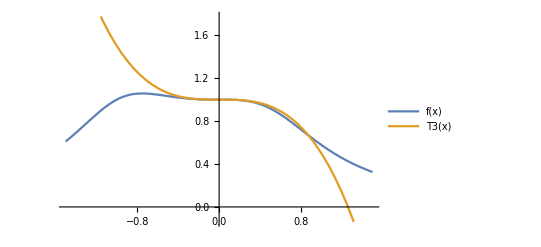

```mathematica
Plot[{f[x],T3[x]},{x,-1.5,1.5},PlotLegends->"Expressions"]
```

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=1/(Sqrt[x^4+x^3+1])
```

```mathematica
Function[x,1/(√(x^4+x^3+1))]
```

Function[x,1/(√(x^4+x^3+1))]

```mathematica
T3v2[x_]=Series[f[x],{x,1,3}]//Normal
```

1/(√3)-(7 (-1+x))/(6 √3)+(13 (-1+x)^2)/(24 √3)+(193 (-1+x)^3)/(432 √3)

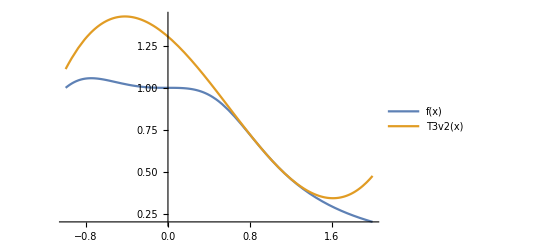

```mathematica
Plot[{f[x],T3v2[x]},{x,-1,2},PlotLegends->"Expressions"]
```

```mathematica
Clear[f,x,T3,T3v2]
```

```mathematica
f[x_]:=1/(Sqrt[x^4+x^3+1])
```

```mathematica
Function[x,1/(√(x^4+x^3+1))]
```

Function[x,1/(√(x^4+x^3+1))]

```mathematica
T3[x_]=Series[f[x],{x,-1,3}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3

```mathematica
T5[x_]=Series[f[x],{x,-1,5}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3+331/128 (1+x)^4+183/256 (1+x)^5

```mathematica
T7[x_]=Series[f[x],{x,-1,7}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3+331/128 (1+x)^4+183/256 (1+x)^5-(6189 (1+x)^6)/1024-(2135 (1+x)^7)/2048

```mathematica
T9[x_]=Series[f[x],{x,-1,9}]//Normal
```

1+(1+x)/2-9/8 (1+x)^2-7/16 (1+x)^3+331/128 (1+x)^4+183/256 (1+x)^5-(6189 (1+x)^6)/1024-(2135 (1+x)^7)/2048+(481395 (1+x)^8)/32768+(64811 (1+x)^9)/65536

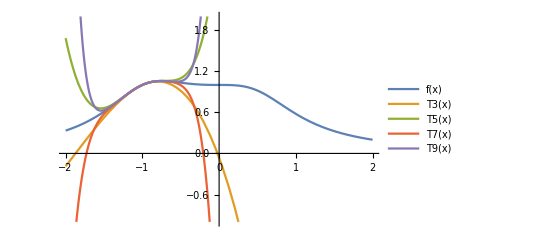

```mathematica
Plot[{f[x],T3[x],T5[x],T7[x],T9[x]},{x,-2,2},PlotLegends->"Expressions",PlotRange->{-1,2}]
```

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=x*Exp[-2x]
```

```mathematica
Function[x,x Exp[-2 x]]
```

Function[x,x Exp[-2 x]]

```mathematica
TaylorList=Table[SeriesCoefficient[f[x],{x,0,n}],{n,0,10}]
```

{0,1,-2,2,-4/3,2/3,-4/15,4/45,-8/315,2/315,-4/2835}

```mathematica
a[n_]=FindSequenceFunction[TaylorList,n]
```

((-1)^n 2^(-2+n))/Pochhammer[1,-2+n]

```mathematica
SumConvergence[a[n]x^n,n]
```

True

```mathematica
Clear[f,x,T3,T5,T7,T9]
```

```mathematica
T3[x_]=Series[Sin[x],{x,0,3}]//Normal
```

x-x^3/6

```mathematica
T3[0.3]
```

0.2955

```mathematica
Sin[c]/(4!)*(.3^4)
```

0.0003375 Sin[c]

```mathematica
Abs[Sin[0.3]-T3[0.3]]
```

0.0000202067

```mathematica
Table[{n,((Pi/4)^(n+1))/((n+1)!)},{n,4,8}]//TableForm//N
```

4. | 0.00249039
5. | 0.000325992
6. | 0.0000365762
7. | 3.59086×10^-6
8. | 3.13362×10^-7

```mathematica
T6[x_]=Series[Cos[x],{x,Pi/4,6}]//Normal
```

1/(√2)-(-π/4+x)/(√2)-(-π/4+x)^2/(2 √2)+(-π/4+x)^3/(6 √2)+(-π/4+x)^4/(24 √2)-(-π/4+x)^5/(120 √2)-(-π/4+x)^6/(720 √2)

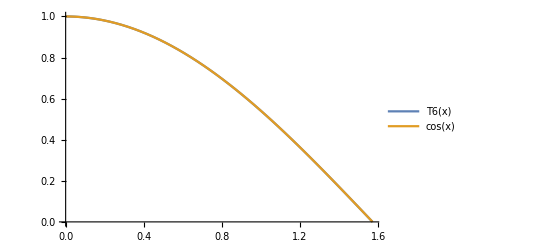

```mathematica
Plot[{T6[x],Cos[x]},{x,0,Pi/2},PlotLegends->"Expressions"]
```

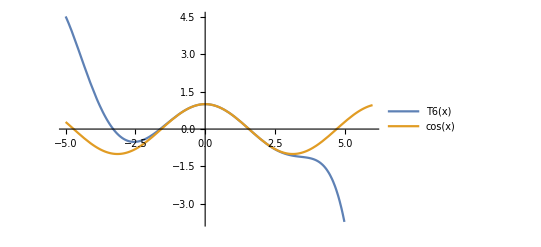

```mathematica
Plot[{T6[x],Cos[x]},{x,-5,6},PlotLegends->"Expressions"]
```